```mathematica
ClearAll["Global`*"]
```

```mathematica
i=2; (*number of days to simulate*)

μ=48; d=0.00025;c=0.00025;(*sets parameters*) (*from 2008 paper*)
(*d = death rate of RBCs - what about bystander killing? Cromer et al. est. is 0.0095 for first six days of infection*)

βRA=6.75 ; βRB=6.75(*0.00015*); 
βNA=2.25; βNB=2.25;
ωR=9;ωE=9;(*Burst sizes for reticulocytes and normocytes, from July 2017 paper *)

θ=0.1; θan=0.52509; (*recovery coefficient for erythropoesis, from 2008 paper*)

τ=2; (*lag time for erythropoesis, from 2008 paper*)
κ=6000000; (*steady state RBC density, from Cromer paper*)
```

```mathematica
(*Initial conditions at time of transfusion*)
PAnext=0 (*(1578+50346)*ωR*0.46;*)
PBnext=(249+135)*ωR*0.46; (*Number of transfused cells that are infected x burst size*)
RA1next=((5920000*0.03)/3);
RA2next=((5920000*0.03)/3);
RA3next=((5920000*0.03)/3); (*0.000802288*)
RB1next=(1062/3);
RB2next=(1062/3);
RB3next=(1062/3);
ErAnext=5920000*0.97;
ErBnext=181628;
IAAnext=0(*1578*0.64;*) (*64% of parasites in ring-stage? i.e., not bursting till next day?*)
IABnext=0;
IBAnext=0;
IBBnext=249*0.64;
InfNAAnext=0(*50346*0.64*);
InfNABnext=0;
InfNBAnext=0;
InfNBBnext=135*0.64;

(*Creates empty lists*)
PAlist={};
PBlist={};
RAlist={};
RBlist={};
ErAlist={};
ErBlist={};
IBAlist={};
IBBlist={};
```

0

0

```mathematica
(*'loops' through days of infection where invasion processes are continuous within each day and aging is discrete at the end of each day*)
Do[{
(*defines continuous invasion dynamics as well as initial densities at the start of each day*)
sys={
PA'[t]== -PA[t]*(βRA*(RA1[t]+RA2[t]+RA3[t]+IAA[t]+IBA[t])+βRB*(RB1[t]+RB2[t]+RB3[t]+IAB[t]+IBB[t])+
βNA*(ErA[t]+InfNAA[t]+InfNBA[t])+βNB*(ErB[t]+InfNAB[t]+InfNBB[t]))-μ*PA[t],
PB'[t]== -PB[t]*(βRA*(RA1[t]+RA2[t]+RA3[t]+IAA[t]+IBA[t])+βRB*(RB1[t]+RB2[t]+RB3[t]+IAB[t]+IBB[t])+
βNA*(ErA[t]+InfNAA[t]+InfNBA[t])+βNB*(ErB[t]+InfNAB[t]+InfNBB[t]))-μ*PB[t],
RA1'[t]==-βRA*PA[t]*RA1[t]-βRA*PB[t]*RA1[t],
RA2'[t]==-βRA*PA[t]*RA2[t]-βRA*PB[t]*RA2[t],
RA3'[t]==-βRA*PA[t]*RA3[t]-βRA*PB[t]*RA3[t],
RB1'[t]==-βRB*PA[t]*RB1[t]-βRB*PB[t]*RB1[t],
RB2'[t]==-βRB*PA[t]*RB2[t]-βRB*PB[t]*RB2[t],
RB3'[t]==-βRB*PA[t]*RB3[t]-βRB*PB[t]*RB3[t],
ErA'[t]==-βNA*PA[t]*ErA[t]-βNA*PB[t]*ErA[t],
ErB'[t]==-βNB*PA[t]*ErB[t]-βNB*PB[t]*ErB[t],
IAA'[t]== βRA*PA[t]*(RA1[t]+RA2[t]+RA3[t]),
IAB'[t]== βRB*PA[t]*(RB1[t]+RB2[t]+RB3[t]),
IBA'[t]== βRA*PB[t]*(RA1[t]+RA2[t]+RA3[t]),
IBB'[t]== βRB*PB[t]*(RB1[t]+RB2[t]+RB3[t]),
InfNAA'[t]== PA[t]*(βNA*ErA[t]),
InfNAB'[t]== PA[t]*(βNB*ErB[t]),
InfNBA'[t]== PB[t]*(βNA*ErA[t]),
InfNBB'[t]== PB[t]*(βNB*ErB[t]),
PA[0]==PAnext,
PB[0]==PBnext,
RA1[0]==RA1next,
RA2[0]==RA2next,
RA3[0]==RA3next,
RB1[0]==RB1next,
RB2[0]==RB2next,
RB3[0]==RB3next,
ErA[0]==ErAnext,
ErB[0]==ErBnext,
IAA[0]==IAAnext,
IAB[0]==IABnext,
IBA[0]==IBAnext,
IBB[0]==IBBnext,
InfNAA[0]==InfNAAnext,
InfNAB[0]==InfNABnext,
InfNBA[0]==InfNBAnext,
InfNBB[0]==InfNBBnext};

(*Solve system of equations*)
sol=NDSolve[sys, {PA,PB,RA1,RA2, RA3,RB1,RB2, RB3,  ErA,ErB, IAA,IAB,IBA,IBB, InfNAA,InfNAB,InfNBA ,InfNBB},{t,0,100}];

(*Store output for t = 0, 0.01 and 0.5*)
AppendTo[PAlist,{PA[0]/.sol,PA[0.01]/.sol,PA[0.5]/.sol}];
AppendTo[PBlist,{PB[0]/.sol,PB[0.01]/.sol,PB[0.5]/.sol}];
AppendTo[RAlist,{(RA1[0]/.sol)+(RA2[0]/.sol)+(RA3[0]/.sol),(RA1[0.01]/.sol)+(RA2[0.01]/.sol)+(RA3[0.01]/.sol),(RA1[0.5]/.sol)+(RA2[0.5]/.sol)+(RA3[0.5]/.sol)}];
AppendTo[RBlist,{(RB1[0]/.sol)+(RB2[0]/.sol)+(RB3[0]/.sol),(RB1[0.01]/.sol)+(RB2[0.01]/.sol)+(RB3[0.01]/.sol),(RB1[0.5]/.sol)+(RB2[0.5]/.sol)+(RB3[0.5]/.sol)}];
AppendTo[ErAlist,{ErA[0]/.sol,ErA[0.01]/.sol,ErA[0.5]/.sol}];
AppendTo[ErBlist,{ErB[0]/.sol,ErB[0.01]/.sol,ErB[0.5]/.sol}];
AppendTo[IBAlist, {(IBA[0]/.sol)+(InfNBA[0]/.sol),(IBA[0.01]/.sol)+(InfNBA[0.01]/.sol),(IBA[0.5]/.sol)+(InfNBA[0.5]/.sol)}];
AppendTo[IBBlist, {(IBB[0]/.sol)+(InfNBB[0]/.sol),(IBB[0.01]/.sol)+(InfNBB[0.01]/.sol),(IBB[0.5]/.sol)+(InfNBB[0.5]/.sol)}];

(*Clear starting densities so they can be reset with densities from end of current day*)Clear[PAnext, PBnext,RA1next,RA2next,RA3next,RB1next,RB2next,RB3next,ErAnext,ErBnext,IAAnext,IABnext,IBAnext,IBBnext,InfNAAnext,InfNABnext, InfNBAnext,InfNBBnext];

(*Set next-day starting values*)
PAnext=First[((IAA[100]/.sol)+(IAB[100]/.sol)+(InfNAA[100]/.sol)+(InfNAB[100]/.sol))*(1-c)];
PBnext=First[((IBA[100]/.sol)+(IBB[100]/.sol)+(InfNBA[100]/.sol)+(InfNBB[100]/.sol))*(1-c)];
RA1next=First[0.5*(κ-(ErA[0]/.sol)-(RA1[0]/.sol)-(RA2[0]/.sol)-(RA3[0]/.sol))];
RA2next=First[(RA1[100]/.sol)*(1-d)];
RA3next=First[(RA2[100]/.sol)*(1-d)];
RB1next=0;
RB2next=First[(RB1[100]/.sol)*(1-d)];
RB3next=First[(RB2[100]/.sol)*(1-d)];
ErAnext=First[((ErA[100]/.sol)+(RA3[100]/.sol))*(1-d)];
ErBnext=First[((ErB[100]/.sol)+(RB3[100]/.sol))*(1-d)];
IAAnext=0;(*set to zero because burst and contribute to starting parasite densities*)
IABnext=0;
IBAnext=0;
IBBnext=0;
InfNAAnext=0;
InfNABnext=0;
InfNBAnext=0;
InfNBBnext=0;

(*sys is cleared so it can be reset with the new starting densities assigned above*)
Clear[sys];}, 
(*specifies the number of days to 'loop' over*)
{i}];
```

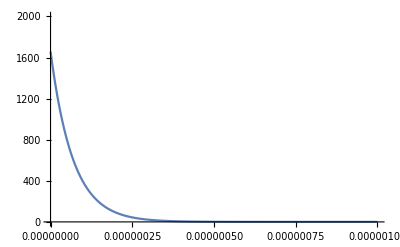

```mathematica
Plot[PB[t]/.sol,{t,0,0.000001}, PlotRange->{0,2000}]
```

```mathematica
PAnext
```

0.

```mathematica
IBBlist
```

{{{245.76},{291.231},{291.231}},{{0.},{52.2732},{52.2732}}}

```mathematica
ErBlist
```

{{{181628.},{181588.},{181588.}},{{181897.},{181850.},{181850.}}}

```mathematica
PAlist
```

{{{0.},{0.},{0.}},{{0.},{0.},{0.}}}

```mathematica
PBlist
```

{{{1413.12},{9.28124×10^-30},{1.30797×10^-52}},{{1658.16},{5.26822×10^-30},{2.02483×10^-53}}}

```mathematica
((IBA[100]/.sol)+(IBB[100]/.sol)+(InfNBA[100]/.sol)+(InfNBB[100]/.sol))*(1-c)
```

{19749.2}

```mathematica
PBnext
```

0.596482